```mathematica
PGamma[n_,p_]:=(-1)^n*Product[If[Mod[k,p]==0,1,k],{k,1,n-1}]
```

```mathematica
L = Table[Reverse[IntegerDigits[Abs[PGamma[3^n,3]],3,30]],{n,1,15}]
```

{{2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2,2,2,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2,2,2,2,1,2,1,0,1,0,0,0,1,1,0,2,0,0,2,2,1,2,0,1,0,2,0,2,0,1},{2,2,2,2,2,1,2,1,2,1,1,2,2,1,0,1,2,2,2,0,2,1,2,2,0,0,1,0,2,0},{2,2,2,2,2,2,1,2,1,2,1,2,0,2,2,1,1,2,0,2,2,0,1,2,1,2,1,1,0,2},{2,2,2,2,2,2,2,1,2,1,2,1,2,2,0,2,2,2,2,0,1,1,1,1,0,1,1,1,0,1},{2,2,2,2,2,2,2,2,1,2,1,2,1,2,2,2,1,2,0,1,1,0,0,0,2,0,2,1,2,1},{2,2,2,2,2,2,2,2,2,1,2,1,2,1,2,2,2,0,2,1,2,2,0,2,0,2,0,1,0,2},{2,2,2,2,2,2,2,2,2,2,1,2,1,2,1,2,2,2,0,1,1,0,2,2,2,2,2,2,2,0},{2,2,2,2,2,2,2,2,2,2,2,1,2,1,2,1,2,2,2,0,1,0,0,0,2,2,0,2,0,2},{2,2,2,2,2,2,2,2,2,2,2,2,1,2,1,2,1,2,2,2,0,1,0,2,2,2,1,0,1,0},{2,2,2,2,2,2,2,2,2,2,2,2,2,1,2,1,2,1,2,2,2,0,1,0,2,1,2,2,2,0},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,2,1,2,1,2,2,2,0,1,0,2,1,1,2,0},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,2,1,2,1,2,2,2,0,1,0,2,1,1,1},{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,2,1,2,1,2,2,2,0,1,0,2,1,1}}

```mathematica
ArrayPlot[L]
```

-Graphics-

```mathematica
L = Table[Reverse[IntegerDigits[Abs[PGamma[3^n,3]]+1,3,30]],{n,2,15}]
```

{{0,0,0,2,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,2,2,1,0,1,0,0,0,1,1,0,2,0,0,2,2,1,2,0,1,0,2,0,2,0,1},{0,0,0,0,0,2,2,1,2,1,1,2,2,1,0,1,2,2,2,0,2,1,2,2,0,0,1,0,2,0},{0,0,0,0,0,0,2,2,1,2,1,2,0,2,2,1,1,2,0,2,2,0,1,2,1,2,1,1,0,2},{0,0,0,0,0,0,0,2,2,1,2,1,2,2,0,2,2,2,2,0,1,1,1,1,0,1,1,1,0,1},{0,0,0,0,0,0,0,0,2,2,1,2,1,2,2,2,1,2,0,1,1,0,0,0,2,0,2,1,2,1},{0,0,0,0,0,0,0,0,0,2,2,1,2,1,2,2,2,0,2,1,2,2,0,2,0,2,0,1,0,2},{0,0,0,0,0,0,0,0,0,0,2,2,1,2,1,2,2,2,0,1,1,0,2,2,2,2,2,2,2,0},{0,0,0,0,0,0,0,0,0,0,0,2,2,1,2,1,2,2,2,0,1,0,0,0,2,2,0,2,0,2},{0,0,0,0,0,0,0,0,0,0,0,0,2,2,1,2,1,2,2,2,0,1,0,2,2,2,1,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,1,2,1,2,2,2,0,1,0,2,1,2,2,2,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,1,2,1,2,2,2,0,1,0,2,1,1,2,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,1,2,1,2,2,2,0,1,0,2,1,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,1,2,1,2,2,2,0,1,0,2,1,1}}

```mathematica
L = Table[Reverse[IntegerDigits[Abs[PGamma[3^(n+1)+1,3]]/Abs[PGamma[3^n+1,3]],3,30]],{n,2,15}]
```

{{0,2,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,2,2,1,0,1,0,0,0,1,1,0,2,0,0,2,2,1,2,0,1,0,2,0,2,0,1,0,2,0},{0,2,2,1,2,1,1,2,2,1,0,1,2,2,2,0,2,1,2,2,0,0,1,0,2,0,1,0,1,0},{0,2,2,1,2,1,2,0,2,2,1,1,2,0,2,2,0,1,2,1,2,1,1,0,2,1,0,0,0,1},{0,2,2,1,2,1,2,2,0,2,2,2,2,0,1,1,1,1,0,1,1,1,0,1,0,2,2,0,1,1},{0,2,2,1,2,1,2,2,2,1,2,0,1,1,0,0,0,2,0,2,1,2,1,0,2,0,2,2,1,0},{0,2,2,1,2,1,2,2,2,0,2,1,2,2,0,2,0,2,0,1,0,2,2,1,2,1,2,2,0,2},{0,2,2,1,2,1,2,2,2,0,1,1,0,2,2,2,2,2,2,2,0,2,1,2,2,1,1,0,2,1},{0,2,2,1,2,1,2,2,2,0,1,0,0,0,2,2,0,2,0,2,1,1,0,2,2,0,1,1,0,1},{0,2,2,1,2,1,2,2,2,0,1,0,2,2,2,1,0,1,0,0,1,2,1,2,0,1,1,2,2,1},{0,2,2,1,2,1,2,2,2,0,1,0,2,1,2,2,2,0,2,0,2,1,2,0,0,1,0,0,2,1},{0,2,2,1,2,1,2,2,2,0,1,0,2,1,1,2,0,0,2,2,2,0,2,1,1,0,2,0,1,1},{0,2,2,1,2,1,2,2,2,0,1,0,2,1,1,1,0,1,1,2,1,1,1,2,2,1,1,2,0,2},{0,2,2,1,2,1,2,2,2,0,1,0,2,1,1,1,2,0,2,1,1,0,2,1,0,1,0,2,2,1}}

```mathematica
ArrayPlot[L]
```

-Graphics-

```mathematica
L2 = Table[Reverse[IntegerDigits[CatalanNumber[3^n],3,30]],{n,2,15}]
```

{{2,0,0,0,0,2,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2,0,2,1,2,2,1,1,0,1,0,1,1,0,2,0,2,0,0,0,1,2,1,0,0,1,0,0,0,1},{2,0,2,0,1,1,1,0,2,1,0,0,1,0,1,1,2,2,0,1,1,1,1,1,0,2,2,2,1,0},{2,0,2,0,0,0,0,2,2,2,1,0,1,2,0,0,1,0,2,2,0,1,2,1,0,0,2,0,2,1},{2,0,2,0,0,2,1,0,1,2,1,1,1,1,2,2,2,1,0,0,0,2,0,2,0,1,1,2,2,1},{2,0,2,0,0,2,0,2,2,0,1,0,1,1,1,2,0,2,1,0,0,1,2,1,1,0,1,2,2,2},{2,0,2,0,0,2,0,1,1,2,2,2,2,2,2,0,0,1,2,1,1,2,1,0,1,2,0,0,0,0},{2,0,2,0,0,2,0,1,0,1,1,1,2,1,1,1,0,0,1,0,0,0,0,0,0,0,2,1,2,0},{2,0,2,0,0,2,0,1,0,0,0,0,1,1,0,0,1,2,1,1,1,2,0,0,1,0,1,0,1,1},{2,0,2,0,0,2,0,1,0,0,2,1,2,2,2,1,2,2,0,1,1,0,0,2,1,0,0,0,0,2},{2,0,2,0,0,2,0,1,0,0,2,0,1,1,1,1,1,1,1,0,1,2,2,0,0,2,0,1,1,1},{2,0,2,0,0,2,0,1,0,0,2,0,0,0,0,0,1,0,0,1,0,2,1,2,0,0,2,2,2,1},{2,0,2,0,0,2,0,1,0,0,2,0,0,2,1,1,2,2,1,2,0,1,1,1,2,2,1,0,1,1},{2,0,2,0,0,2,0,1,0,0,2,0,0,2,0,0,1,1,1,1,2,1,0,1,1,1,1,2,0,2}}

```mathematica
ArrayPlot[L2]
```

-Graphics-

```mathematica
L3 = Table[Reverse[IntegerDigits[Fibonacci[2^(2n+1)],2,35]],{n,2,13}];
```

```mathematica
ArrayPlot[L3]
```

-Graphics-

```mathematica
?PolynomialMod
```

PolynomialMod[poly,m] gives the polynomial poly reduced modulo m. 
PolynomialMod[poly,{m_1,m_2,…}] reduces modulo all of the m_i.

```mathematica
PolynomialMod[x^3,x^2+1]
```

-x

```mathematica
PolynomialMod[10/3,8]
```

6

```mathematica
PowerMod[3,-1,8]
```

3

```mathematica
L4 = Table[Reverse[IntegerDigits[PolynomialMod[(Abs[PGamma[2^(n+1)+1,2]]/((Abs[PGamma[2^n+1,2]])^2)-1)/2^n,2^30],2,30]],{n,2,20}]
```

{{0,0,1,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1,1},{0,0,0,1,1,0,1,1,0,0,1,0,1,1,0,0,1,0,1,1,0,0,1,0,1,1,0,0,1,0},{0,0,0,0,1,1,1,0,1,1,0,1,0,0,1,0,0,0,0,0,0,0,1,1,0,1,0,0,0,1},{0,0,0,0,0,1,1,1,1,0,1,1,0,1,1,0,1,0,1,0,1,1,0,0,0,1,1,1,0,0},{0,0,0,0,0,0,1,1,1,1,1,0,1,1,0,1,1,1,1,1,1,0,0,1,1,1,0,0,1,1},{0,0,0,0,0,0,0,1,1,1,1,1,1,0,1,1,0,1,1,1,0,0,1,0,1,1,0,1,0,1},{0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,0,1,1,0,1,1,1,0,1,1,1,0,1,1,1},{0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,0,1,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,0,1,0,1},{0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1}}

```mathematica
ArrayPlot[L4]
```

-Graphics-

```mathematica
L5 = Table[Reverse[IntegerDigits[CatalanNumber[2^n],2,30]],{n,2,15}]
```

{{0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,0,1,0,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,0,0,1,1,1,1,1,0,0,0,0,0,1,1,1,0,1,1,0,0,0,0,1,0,0,0,0},{0,1,1,0,0,0,0,1,1,0,0,0,1,0,0,0,0,1,1,1,0,1,1,1,1,0,0,0,1,0},{0,1,1,0,0,0,1,1,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,1,0,1,0,0,1,1},{0,1,1,0,0,0,1,0,1,1,1,1,1,0,0,1,0,0,1,0,0,1,1,0,1,1,0,1,1,0},{0,1,1,0,0,0,1,0,0,0,1,1,1,1,1,1,1,1,1,0,1,1,0,1,0,1,1,1,0,0},{0,1,1,0,0,0,1,0,0,1,1,0,1,1,0,1,1,1,1,0,0,0,1,0,1,1,1,1,1,1},{0,1,1,0,0,0,1,0,0,1,0,1,0,1,0,0,1,1,0,1,0,0,0,0,0,1,0,0,0,1},{0,1,1,0,0,0,1,0,0,1,0,0,1,0,0,0,0,1,0,0,0,1,0,0,0,1,1,1,1,1},{0,1,1,0,0,0,1,0,0,1,0,0,0,1,1,1,1,1,1,1,0,0,0,1,0,0,0,0,1,0},{0,1,1,0,0,0,1,0,0,1,0,0,0,0,0,1,1,1,0,1,0,1,1,0,0,1,1,1,1,0},{0,1,1,0,0,0,1,0,0,1,0,0,0,0,1,1,0,1,0,0,0,1,0,0,0,1,1,1,1,0},{0,1,1,0,0,0,1,0,0,1,0,0,0,0,1,0,1,0,0,0,1,0,0,1,1,0,1,1,0,1}}

```mathematica
ArrayPlot[L5]
```

-Graphics-

```mathematica
L6 = Table[Reverse[IntegerDigits[PolynomialMod[CatalanNumber[3^n+3^(n-1)],3^30],3,30]],{n,2,10}];
```

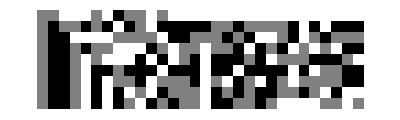

```mathematica
ArrayPlot[L6]
```

```mathematica
L7 = Table[Reverse[IntegerDigits[PolynomialMod[2*CatalanNumber[3^n],3^30],3,30]],{n,2,10}];
```

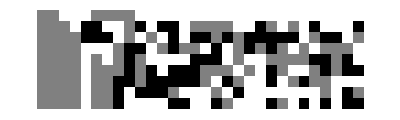

```mathematica
ArrayPlot[L7]
```

```mathematica
NewFactPower[n_]:=(-1)^(n)*(2^(2^n-1))Product[PGamma[2^(n-k)+1,2],{k,0,n}]
```

```mathematica
Table[Factorial[2^n]/(NewFactPower[n]),{n,0,14}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
Catalimit[n_,digits_]:=PolynomialMod[(-1)^(n+1)*2*PGamma[2^(n+1)+1,2]/Product[PGamma[2^(n-k)+1,2],{k,0,n}],2^digits]
```

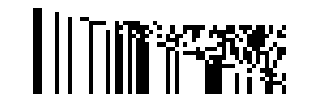

```mathematica
ArrayPlot[Table[Reverse[IntegerDigits[Catalimit[n,60],2]],{n,1,20}]]
```

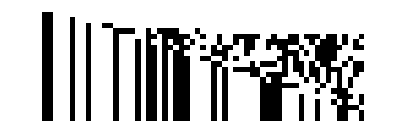

```mathematica
ArrayPlot[Table[Reverse[IntegerDigits[Catalimit2[n,60],2]],{n,1,20}]]
```

```mathematica
ArrayPlot[Table[Reverse[IntegerDigits[CatalanNumber[2^n],2,30]],{n,0,13}]]
```

-Graphics-

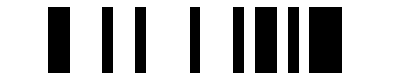

```mathematica
ArrayPlot[{Last[Table[Reverse[IntegerDigits[Catalimit[n,30],2]],{n,1,15}]],Reverse[IntegerDigits[CatalanNumber[2^29],2,30]]}]
```

```mathematica
Table[StirlingS1[n,0],{n,0,10}]
```

{1,0,0,0,0,0,0,0,0,0,0}

```mathematica
Catalimit2[n_,digits_]:=PolynomialMod[2*PGamma[2^(n+1),2]/Product[PGamma[2^(k),2],{k,1,n}],2^digits]
```

```mathematica
ArrayPlot[Table[Reverse[IntegerDigits[PGamma[2^n+1,2],2,30]],{n,1,13}]]
```

-Graphics-

```mathematica
ArrayPlot[Table[Reverse[IntegerDigits[Product[PGamma[2^k+1,2],{k,1,n}],2,30]],{n,1,25}]]
```

-Graphics-

```mathematica
ArrayPlot[Table[Reverse[IntegerDigits[Product[PGamma[2^k+1,2],{k,1,n}],2,30]],{n,30,30}]]
```

$Aborted

```mathematica
Test[n_,m_]:=Module[{gamma=PGamma[2^m,2]},Product[gamma^((2^k)*(n-m-k+1)),{k,0,n-m}]]
```

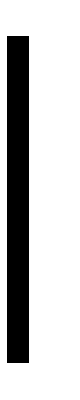

```mathematica
ArrayPlot[Table[Reverse[IntegerDigits[PolynomialMod[Test[n,3],2^3],2,3]],{n,1,25}]]
```

```mathematica
L3 = Table[Reverse[IntegerDigits[(3^(2^n)-1)/2^n,2,35]],{n,0,20}];
```

```mathematica
ArrayPlot[L3]
```

-Graphics-